# Boats Boats Boats

### Defining Variables

```mathematica
Clear[f,density,xmin1,xmax1,ymin1,ymax1,zmin1,zmax1,xballast,yballast,ballastmass, θ, boat, water, submerged, boatmass, totalmass, xcomboat, ycomboat, xcom, ycom, displacement, waterline, b, d, draft, cob, xcob, ycob, x, y, z]
Clear["Global`*"]
f = 2*((x/2)^2);
density =300;
ballastmass = 5000;
xmin1 = -2;
xmax1 = 2;
ymin1 = 0;
ymax1 = 2;
zmin1 = 0;
zmax1 =10;
xballast = 0;
yballast = 0;
θ = 30Degree;
```

### 3D Plot of Boat’s submerged region (ESTIMATE. NOT ACTUALLY)

```mathematica
RegionPlot3D[zmin1≤z≤zmax1&&f≤y≤Tan[θ]*x+1&&xmin1≤x≤xmax1, {x, -5, 5},{y, 0, 10},{z, zmin1, zmax1}, PlotPoints->100,  Axes->True, AxesLabel->{x, y, z}]
```

-Graphics3D-

### Defining Boat region

```mathematica
boat = ImplicitRegion[f<y<ymax1&&xmin1<x<xmax1&&ymin1<y<ymax1, {x,y}]
```

ImplicitRegion[x^2/2<y<2&&-2<x<2&&0<y<2,{x,y}]

### Defining water region

```mathematica
water = ImplicitRegion[ymin1<y<Tan[θ]*x+b&&xmin1<x<xmax1&&ymin1<y<ymax1, {x,y}]
```

ImplicitRegion[0<y<b+x/(√3)&&-2<x<2&&0<y<2,{x,y}]

### Defining Submerged region of boat as intersection of boat and water

ImplicitRegion[-2<x<2&&0<y<2&&0<y<b+x/(√3)&&x^2/2<y<2,{x,y}]

-Graphics-

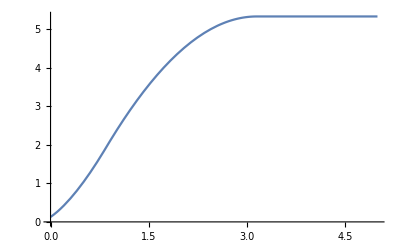

```mathematica
submerged = RegionIntersection[boat, water]
RegionPlot[submerged/. b->5]
Plot[RegionMeasure[submerged/.b->bb],{bb,0,5}]
```

### Figuring out total mass of boat by integration and adding ballastmass

∈ sign is escape, e, l, escape

```mathematica
boatmass = 10*Integrate[density,{x, y}∈boat]
```

16000

```mathematica
totalmass = boatmass+ballastmass
```

21000

### Finding COMs

```mathematica
xcomboat = ( 1/boatmass)*10*Integrate[x*density,{x, y}∈boat]
```

0

Just boat

```mathematica
ycomboat = N[( 1/boatmass)*10*Integrate[y*density,{x, y}∈boat]]
```

1.2

COM of combined boat and ballast: 2 ways, second one takes into account ballast x or y coordinate

```mathematica
xcom = N[( 1/totalmass)*10*Integrate[x*density,{x, y}∈boat]]
xcom = 1/(total)*(xcomboat*boatmass+xballast*ballastmass)
```

0.

0

```mathematica
ycom = N[( 1/totalmass)*10*Integrate[y*density,{x, y}∈boat]]
ycom = 1/(totalmass)*(ycomboat*boatmass+yballast*ballastmass)
```

0.914286

0.914286

### Finding Buoyant force with b as a variable

10. (Piecewise[{{74.0741 (1.73205 √(1.+6. b)+10.3923 b √(1.+6. b)), -0.166667<b≤0.845299}, {-18.5185 (46.5256-155.885 b+46.7654 b^2-3.4641 √(1.+6. b)-20.7846 b √(1.+6. b)), 0.845299<b<1.1547||1.1547≤b<3.1547}, {1000. (2. (2.+1.73205 (-2.+b))+0.166667 (-8.-5.19615 (-2.+b)^3)), b==3.1547}, {5333.33, b>3.1547}, {0., True}}])

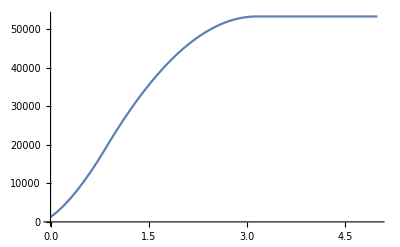

```mathematica
displacement = N[10*Integrate[1000,{x, y}∈submerged]]
Plot[displacement/. b->bb, {bb, 0, 5}]
```

### Figuring out waterline based on displacement

```mathematica
waterline = Solve[displacement == mass, b, Reals];
waterline/.mass->totalmass
draft = b/.%[[4]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{b→Undefined},{b→Undefined},{b→Undefined},{b→0.909465}}

0.909465

### Finding Center of buoyancy

```mathematica
cob = N[10*Integrate[1000*{x, y}, {x,y}∈submerged]/displacement];
xycob = cob/.b->draft
xcob=xycob[[1]]
ycob=xycob[[2]]
```

{0.574017,0.809448}

0.574017

0.809448

### Plotting boat with waterline

{{0.574017,0.809448}}

{{0,0.914286}}

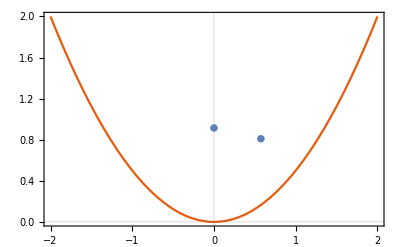

```mathematica
plotcob = {{xcob,ycob}}
plotcom = {{xcom, ycom}}
Show[Plot[f, {x,xmin1,xmax1},PlotRange->{{xmin1,xmax1},{ymin1,ymax1}}, PlotTheme->"Scientific"],ListPlot[plotcob], ListPlot[plotcom],
Plot[Tan[θ]+b, {x,xmin1,xmax1},PlotRange->{{xmin1,xmax1},{ymin1,ymax1}}, PlotTheme->"Scientific"] ]
```

### Calculating Righting Moment

```mathematica
rmx = (xcom-xcob)*totalmass
rmy = (ycom-ycob)*totalmass
```

-12054.4

2201.6

### Results for angles I have run it at:

30: COB = {{0.574017,0.809448}}, RM = (-12054, 2201)
45: COB = {0.771827,0.95692}, RM = (-16208, -895)